```mathematica
α=2.;u0=1.*10^-8;
k:=√(2e);
```

```mathematica
δ50Lepage={-0.000421343353,-0.133227246,-1.319383451,-0.900186195,-0.146570028,-0.654835316,1.232867297,-0.579619620,-1.156444634,-0.106466466,-1.457426179,1.160634967};
```

```mathematica
δ50[V_]:=
Module[{r1=50,r2=u0,sol,δr,δs,δ50r,ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1},jder,nder,β},
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];
β:=r1 u'[r1]/u[r1]-1;
δ50r=Table[
e=ee[[i]];
sol=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs=FindRoot[Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->30,AccuracyGoal->Infinity,PrecisionGoal->20];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&];
δr,{i,1,12}]
]
```

```mathematica
δ501=δ50[-1.3862179318475605/#^1.2152447118079408&];
δ502=δ50[-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&];
δ503=δ50[-0.39300593613292306/#^1.5993730406518318-1/#&];
δ504=δ50[-1/#-(0.7938946124458129 ⅇ^(-0.7393687788904056 #^2))/#&];
δ505=δ50[-1/#-(0.8754087795254966 ⅇ^(-0.8650251771559941 #))/#-(0.12000884535063085 ⅇ^(-2.5072729196893575 #^2))/#&];
δ506=δ50[0.04522449237809833-1/#-(1.0198492477920686 ⅇ^(-1.167952723017384#))/#-0.1100914875072552/#^0.6089330485249438&];
N[{δ501,δ502,δ503,δ504,δ505,δ506},6]//TableForm
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1.38622 Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1.38622 Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1.38622 Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==1.17774) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.71351) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==1.87919) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.616853) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-15.5631) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==0.0432091) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+0.393006 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+0.393006 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+0.393006 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==0.973279) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-1.06777) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==0.622737) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+0.793895 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r+0.793895 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r+0.793895 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-2.62353) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==4.30546) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.0683328) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+0.875409 Power[«2»] Power[«2»]+0.120009 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r+0.875409 Power[«2»] Power[«2»]+0.120009 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r+0.875409 Power[«2»] Power[«2»]+0.120009 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.531046) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-11.5881) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==0.0526) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

NDSolve::precw: 参数函数的精度 ({{2. (-0.0452245+1/r+1.01985 Power[«2»] Power[«2»]+0.110091 Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (-0.0452145+1/r+1.01985 Power[«2»] Power[«2»]+0.110091 Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (-0.0442245+1/r+1.01985 Power[«2»] Power[«2»]+0.110091 Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==2.49331) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.21487) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==0.557794) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

-0.000739519 | -0.233785 | 0.866835 | -0.619736 | 1.08177 | 0.634869 | -1.55685 | -0.134742 | -0.871331 | 0.121337 | -1.28177 | 1.33609
-0.000211093 | -0.0662107 | -0.552719 | -1.50663 | 0.0431822 | -0.863664 | -0.167926 | 0.718729 | -0.109909 | 0.598061 | -1.00407 | 1.54767
-0.000768608 | -0.242983 | 0.771857 | -0.818161 | 0.556971 | -0.25948 | 0.537381 | 1.56746 | 0.64437 | 1.26243 | -0.443878 | -1.08169
-0.000474917 | -0.149895 | -1.20663 | 1.34258 | -0.0682268 | -0.956136 | -0.308528 | 0.579904 | -0.243092 | 0.463324 | -1.11923 | 1.44321
-0.000154685 | -0.0484279 | -0.488175 | -1.48471 | 0.0525516 | -0.855439 | -0.155998 | 0.730444 | -0.0992678 | 0.606355 | -0.999551 | 1.55055
-0.00061917 | -0.195793 | 1.18936 | -0.211652 | 0.508808 | 0.11885 | -1.24581 | 1.03065 | 0.549548 | -0.961176 | 1.09982 | 0.667775

```mathematica
{(δ501-δ50Lepage),(δ502-δ50Lepage),(δ503-δ50Lepage),(δ504-δ50Lepage),(δ505-δ50Lepage),(δ506-δ50Lepage)}//TableForm
```

-0.000318176 | -0.100558 | 2.18622 | 0.28045 | 1.22834 | 1.2897 | -2.78972 | 0.444878 | 0.285113 | 0.227804 | 0.175654 | 0.175452
0.00021025 | 0.0670166 | 0.766664 | -0.606444 | 0.189752 | -0.208829 | -1.40079 | 1.29835 | 1.04654 | 0.704527 | 0.453356 | 0.387031
-0.000347265 | -0.109756 | 2.09124 | 0.0820252 | 0.703541 | 0.395355 | -0.695486 | 2.14708 | 1.80081 | 1.3689 | 1.01355 | -2.24233
-0.0000535735 | -0.0166679 | 0.112752 | 2.24277 | 0.0783433 | -0.3013 | -1.5414 | 1.15952 | 0.913353 | 0.56979 | 0.338201 | 0.282575
0.000266658 | 0.0847993 | 0.831209 | -0.584528 | 0.199122 | -0.200604 | -1.38887 | 1.31006 | 1.05718 | 0.712821 | 0.457875 | 0.38991
-0.000197827 | -0.0625662 | 2.50875 | 0.688534 | 0.655378 | 0.773686 | -2.47868 | 1.61027 | 1.70599 | -0.85471 | 2.55725 | -0.49286

```mathematica
{(δ501-δ50Lepage),(δ502-δ50Lepage),(δ503-δ50Lepage),(δ504-δ50Lepage),(δ505-δ50Lepage),(δ506-δ50Lepage)}//TableForm
```

-0.000318176 | -0.100558 | 2.18622 | 0.28045 | 1.22834 | 1.2897 | -2.78972 | 0.444878 | 0.285113 | 0.227804 | 0.175654 | 0.175452
0.00021025 | 0.0670166 | 0.766664 | -0.606444 | 0.189752 | -0.208829 | -1.40079 | 1.29835 | 1.04654 | 0.704527 | 0.453356 | 0.387031
-0.000347265 | -0.109756 | 2.09124 | 0.0820252 | 0.703541 | 0.395355 | -0.695486 | 2.14708 | 1.80081 | 1.3689 | 1.01355 | -2.24233
-0.0000535735 | -0.0166679 | 0.112752 | 2.24277 | 0.0783433 | -0.3013 | -1.5414 | 1.15952 | 0.913353 | 0.56979 | 0.338201 | 0.282575
0.000266658 | 0.0847993 | 0.831209 | -0.584528 | 0.199122 | -0.200604 | -1.38887 | 1.31006 | 1.05718 | 0.712821 | 0.457875 | 0.38991
-0.000197827 | -0.0625662 | 2.50875 | 0.688534 | 0.655378 | 0.773686 | -2.47868 | 1.61027 | 1.70599 | -0.85471 | 2.55725 | -0.49286

```mathematica
{NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ501-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ502-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ503-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ504-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ505-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ506-δ50Lepage)}//TableForm
```

-0.000318176 | -0.100558 | -0.955374 | 0.28045 | 1.22834 | 1.2897 | 0.351875 | 0.444878 | 0.285113 | 0.227804 | 0.175654 | 0.175452
0.00021025 | 0.0670166 | 0.766664 | -0.606444 | 0.189752 | -0.208829 | -1.40079 | 1.29835 | 1.04654 | 0.704527 | 0.453356 | 0.387031
-0.000347265 | -0.109756 | -1.05035 | 0.0820252 | 0.703541 | 0.395355 | -0.695486 | -0.994514 | -1.34078 | 1.3689 | 1.01355 | 0.899266
-0.0000535735 | -0.0166679 | 0.112752 | -0.898827 | 0.0783433 | -0.3013 | -1.5414 | 1.15952 | 0.913353 | 0.56979 | 0.338201 | 0.282575
0.000266658 | 0.0847993 | 0.831209 | -0.584528 | 0.199122 | -0.200604 | -1.38887 | 1.31006 | 1.05718 | 0.712821 | 0.457875 | 0.38991
-0.000197827 | -0.0625662 | -0.632845 | 0.688534 | 0.655378 | 0.773686 | 0.662915 | -1.53132 | -1.4356 | -0.85471 | -0.584345 | -0.49286

```mathematica
Abs@{NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ501-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ502-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ503-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ504-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ505-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ506-δ50Lepage)}//TableForm
Mean@#&/@%
```

0.000318176 | 0.100558 | 0.955374 | 0.28045 | 1.22834 | 1.2897 | 0.351875 | 0.444878 | 0.285113 | 0.227804 | 0.175654 | 0.175452
0.00021025 | 0.0670166 | 0.766664 | 0.606444 | 0.189752 | 0.208829 | 1.40079 | 1.29835 | 1.04654 | 0.704527 | 0.453356 | 0.387031
0.000347265 | 0.109756 | 1.05035 | 0.0820252 | 0.703541 | 0.395355 | 0.695486 | 0.994514 | 1.34078 | 1.3689 | 1.01355 | 0.899266
0.0000535735 | 0.0166679 | 0.112752 | 0.898827 | 0.0783433 | 0.3013 | 1.5414 | 1.15952 | 0.913353 | 0.56979 | 0.338201 | 0.282575
0.000266658 | 0.0847993 | 0.831209 | 0.584528 | 0.199122 | 0.200604 | 1.38887 | 1.31006 | 1.05718 | 0.712821 | 0.457875 | 0.38991
0.000197827 | 0.0625662 | 0.632845 | 0.688534 | 0.655378 | 0.773686 | 0.662915 | 1.53132 | 1.4356 | 0.85471 | 0.584345 | 0.49286

{0.459626,0.594126,0.721155,0.517732,0.601437,0.697913}

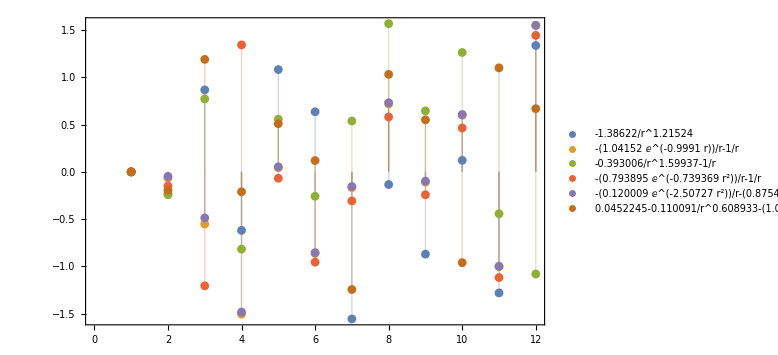

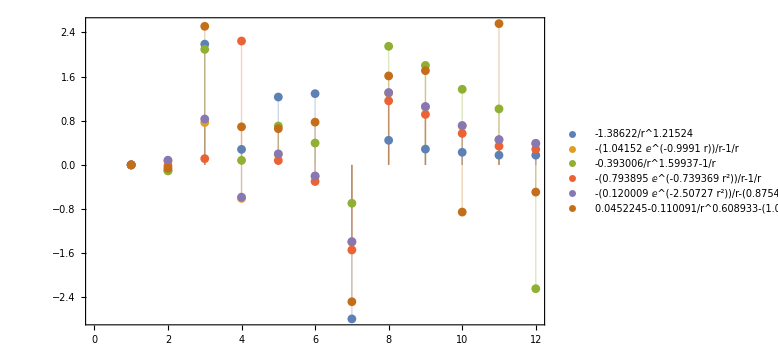

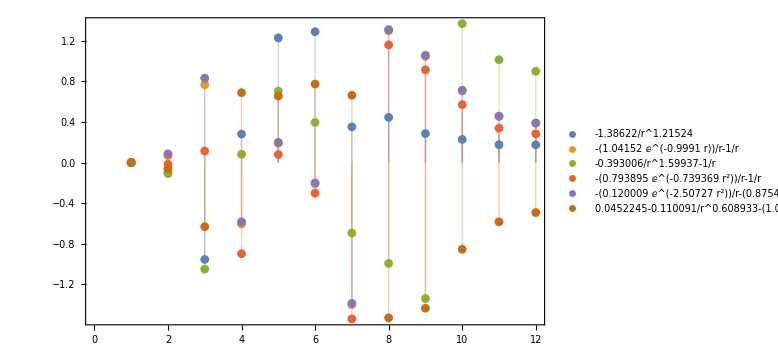

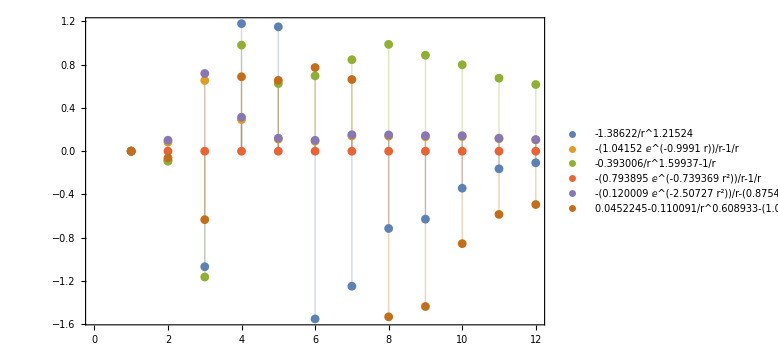

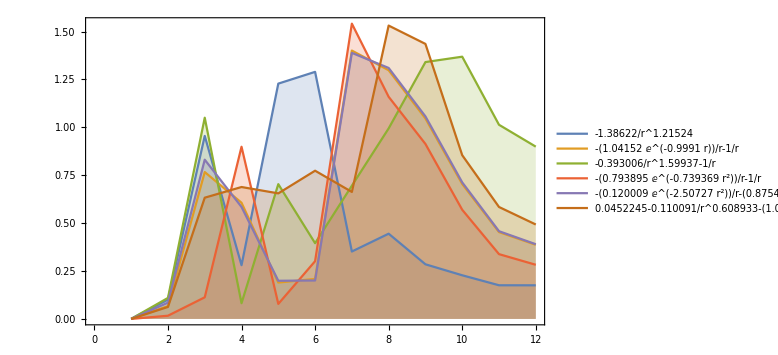

```mathematica
ListPlot[{δ501,δ502,δ503,δ504,δ505,δ506},Filling->Axis,Frame->True,ImageSize->Large,PlotLegends->{-1.3862179318475605/#^1.2152447118079408&[r],-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&[r],-0.39300593613292306/#^1.5993730406518318-1/#&[r],-1/#-(0.7938946124458129 ⅇ^(-0.7393687788904056 #^2))/#&[r],-1/#-(0.8754087795254966 ⅇ^(-0.8650251771559941 #))/#-(0.12000884535063085 ⅇ^(-2.5072729196893575 #^2))/#&[r],0.04522449237809833-1/#-(1.0198492477920686 ⅇ^(-1.167952723017384#))/#-0.1100914875072552/#^0.6089330485249438&[r]},Joined->False]
ListPlot[{(δ501-δ50Lepage),(δ502-δ50Lepage),(δ503-δ50Lepage),(δ504-δ50Lepage),(δ505-δ50Lepage),(δ506-δ50Lepage)},Filling->Axis,Frame->True,ImageSize->Large,PlotLegends->{-1.3862179318475605/#^1.2152447118079408&[r],-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&[r],-0.39300593613292306/#^1.5993730406518318-1/#&[r],-1/#-(0.7938946124458129 ⅇ^(-0.7393687788904056 #^2))/#&[r],-1/#-(0.8754087795254966 ⅇ^(-0.8650251771559941 #))/#-(0.12000884535063085 ⅇ^(-2.5072729196893575 #^2))/#&[r],0.04522449237809833-1/#-(1.0198492477920686 ⅇ^(-1.167952723017384#))/#-0.1100914875072552/#^0.6089330485249438&[r]},Joined->False]
ListPlot[{NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ501-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ502-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ503-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ504-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ505-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ506-δ50Lepage)},Filling->Axis,Frame->True,ImageSize->Large,PlotLegends->{-1.3862179318475605/#^1.2152447118079408&[r],-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&[r],-0.39300593613292306/#^1.5993730406518318-1/#&[r],-1/#-(0.7938946124458129 ⅇ^(-0.7393687788904056 #^2))/#&[r],-1/#-(0.8754087795254966 ⅇ^(-0.8650251771559941 #))/#-(0.12000884535063085 ⅇ^(-2.5072729196893575 #^2))/#&[r],0.04522449237809833-1/#-(1.0198492477920686 ⅇ^(-1.167952723017384#))/#-0.1100914875072552/#^0.6089330485249438&[r]},Joined->False]
ListPlot[{NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ501-δ504),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ502-δ504),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ503-δ504),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ504-δ504),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ505-δ504),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ506-δ50Lepage)},Filling->Axis,Frame->True,ImageSize->Large,PlotLegends->{-1.3862179318475605/#^1.2152447118079408&[r],-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&[r],-0.39300593613292306/#^1.5993730406518318-1/#&[r],-1/#-(0.7938946124458129 ⅇ^(-0.7393687788904056 #^2))/#&[r],-1/#-(0.8754087795254966 ⅇ^(-0.8650251771559941 #))/#-(0.12000884535063085 ⅇ^(-2.5072729196893575 #^2))/#&[r],0.04522449237809833-1/#-(1.0198492477920686 ⅇ^(-1.167952723017384#))/#-0.1100914875072552/#^0.6089330485249438&[r]},Joined->False]
ListPlot[Abs@{NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ501-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ502-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ503-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ504-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ505-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ506-δ50Lepage)},Frame->True,ImageSize->Large,PlotLegends->{-1.3862179318475605/#^1.2152447118079408&[r],-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&[r],-0.39300593613292306/#^1.5993730406518318-1/#&[r],-1/#-(0.7938946124458129 ⅇ^(-0.7393687788904056 #^2))/#&[r],-1/#-(0.8754087795254966 ⅇ^(-0.8650251771559941 #))/#-(0.12000884535063085 ⅇ^(-2.5072729196893575 #^2))/#&[r],0.04522449237809833-1/#-(1.0198492477920686 ⅇ^(-1.167952723017384#))/#-0.1100914875072552/#^0.6089330485249438&[r]},Filling->Axis,Joined->True]
```

```mathematica
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_PhaseShift_delta50comparasion.eps",%17];
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_PhaseShift_delta50comparasion_2.eps",%19];
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_PhaseShift_delta50comparasion_3.eps",%20];
```